# PROBLEM 01

Using PolarPlot:

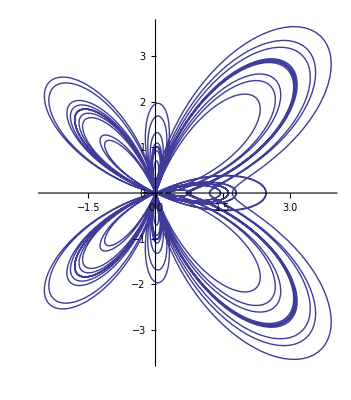

Using ParametricPlot

-Graphics-

```mathematica
Text["Using PolarPlot:"]
PolarPlot[ⅇ^Cos[t]-2*Cos[4*t]+Sin[t/12]^5,{t,0,24*Pi}]

Text["Using ParametricPlot"]
CoordinateTransformData["Polar"->"Cartesian","Mapping", {ⅇ^Cos[θ]-2*Cos[4*θ]+Sin[θ/12]^5,θ}];ParametricPlot[{Cos[θ] (ⅇ^Cos[θ]-2 Cos[4 θ]+Sin[θ/12]^5),(ⅇ^Cos[θ]-2 Cos[4 θ]+Sin[θ/12]^5) Sin[θ]},{θ,0,24*Pi}]
```

# PROBLEM 02

-Graphics3D-

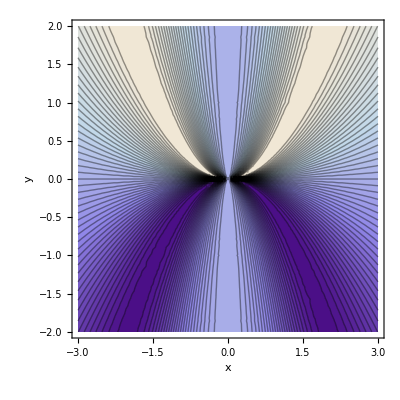

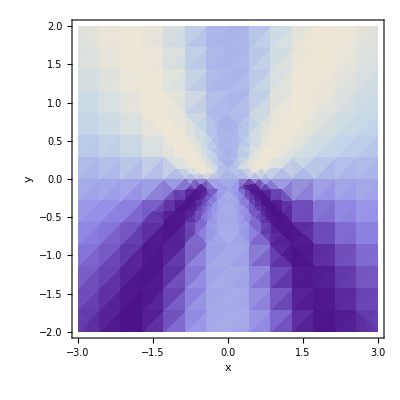

```mathematica
f[x_,y_]:=(x^2*y)/(x^4+4*y^2)
Plot3D[f[x,y],{x,-3,3},{y,-2,2},AxesLabel->{x,y,z},PlotPoints->10,Mesh->All,MaxRecursion->0,PlotStyle->{Orange,Dashed,Thick},ColorFunction->"BlueGreenYellow"]
ContourPlot[f[x,y],{x,-3,3},{y,-2,2},AxesLabel->{x,y,z},Contours->50,Mesh->None]
DensityPlot[f[x,y],{x,-3,3},{y,-2,2},AxesLabel->{x,y,z}]
```

# PROBLEM 03

```mathematica
Plot3D[(10-3*x-y)/5,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

# PROBLEM 04

## (i)

```mathematica
ParametricPlot3D[{Cos[t]*4*Cos[r],2*Sin[r]*Cos[t],Sin[t]},{t,-Pi/2,π/2},{r,-π,π},BoxRatios->{1,1,1}]
```

-Graphics3D-

## (ii)

```mathematica
ContourPlot3D[x^2/16+y^2/4+z^2==1,{x,-4,4},{y,-2,2},{z,-1,1},BoxRatios->{1,1,1},Axes->{0,0,0},BoxRatios->{1,1,1},AxesLabel->{X,Y,Z},Mesh->7]
```

-Graphics3D-

# PROBLEM 05

(i)Ploting function

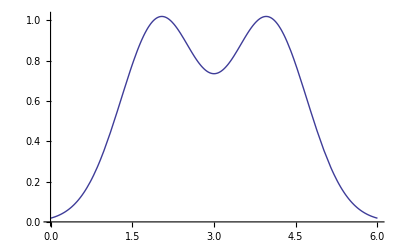

(ii)The volume using cylindrical shell is:

8.76132

(iii) Ploting revolution using RevolutionPlot3D

-Graphics3D-

Ploting revolution using ParametricPlot3D

-Graphics3D-

(iv) Volume revolving with y=f(x),x=1,x=5

61.5638

(v) Using ParametricPlot3D to generate solid

-Graphics3D-

-Graphics3D-

```mathematica
Remove[f,x]



f[x_]:=Exp[-(x-2)^2]+Exp[-(x-4)^2]
Text["(i)Ploting function"]
Plot[f[x],{x,0,6}]
Text["(ii)The volume using cylindrical shell is:"]
Integrate[π*(f[x])^2,{x,1,5}]//N
Text["(iii) Ploting revolution using RevolutionPlot3D"]
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{1,0,0}]
Text["Ploting revolution using ParametricPlot3D"]
ParametricPlot3D[{x,f[x]*Cos[t],f[x]*Sin[t]},{x,1,5},{t,0,2Pi}]
Text["(iv) Volume revolving with y=f(x),x=1,x=5"]
Integrate[2*π*x*f[x],{x,1,5}]//N
Text["(v) Using ParametricPlot3D to generate solid"]
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{0,0,1}]
ParametricPlot3D[{x*Cos[t],f[x]*Sin[t],f[x]},{x,0,4},{t,0,8}]
```

# PROBLEM 06

```mathematica
Remove[x,y]
c=ContourPlot3D[4*x^2+4*y^2==z,{x,-1,1},{y,-1,1},{z,0,16}];
d=ContourPlot3D[16-4*x^2-4*y^2==z,{x,-1,1},{y,-1,1},{z,0,16}];
Show[c,d]

Text["The volume of the solid is="]
Integrate[Abs[4*x^2+4*y^2-16+4*x^2+4*y^2],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

The volume of the solid is=

128/3

# PROBLEM 07

```mathematica
Remove[x,y,z]
ContourPlot3D[4-x^2-y^2==z,{x,-3,3},{y,-3,3},{z,0,5},AxesOrigin->{0,0,0},AxesStyle->Thick,Boxed->False,Mesh->3]
Text["The volume of the solid is="]
Integrate[r*(4-(r*Cos[θ])^2-(r*Sin[θ])^2),{r,0,2},{θ,0,2π}]
```

-Graphics3D-

The volume of the solid is=

8 π

# PROBLEM 08

```mathematica
Remove[x,y,z]
d=ContourPlot3D[z==1-x-y,{x,-1,1},{y,-1,1},{z,-1,1}];
e=ContourPlot3D[z==1+x+y,{x,-1,1},{y,-1,1},{z,-1,1}];
f=ContourPlot3D[y==1-x,{x,-1,1},{y,-1,1},{z,-1,1}];
g=ContourPlot3D[y==0,{x,-1,1},{y,-1,1},{z,-1,1}];
h=ContourPlot3D[x==0,{x,-1,1},{y,-1,1},{z,-1,1}];
Show[d,e,f,g,h,PlotRange->{{0,1},{0,1},{-1,1}},AxesLabel->{X,Y,Z}]
Text["The mass will be equal to="]
Integrate[Abs[1+x+y-1+x+y]*(1+x^2+y^2),{x,0,1},{y,0,1-x}]
```

-Graphics3D-

The mass will be equal to=

14/15

# PROBLEM 09

```mathematica
Remove[x,y,z,f]
f[x_,y_]:=4/(x^2+y^2+1)
x1=1/2;
y1=1;
s1=D[f[x,y],x]/.{x->x1,y->y1};
s2=D[f[x,y],y]/.{x->x1,y->y1};
s3=-1;
Text["The equations are:"]
st=Solve[{s1,s2,s3}.({x,y,z}-{x1,y1,f[x1,y1]})==0,z]//Flatten
sn=Solve[{x,y,z}=={x1,y1,f[x1,y1]}-t{s1,s2,s3},{x,y,z}]//Flatten
p=Plot3D[f[x,y],{x,-2,2},{y,-2,2},ColorFunction->Function[{x,y,z},RGBColor[x,y,z]]];
q=Plot3D[st[[1,2]],{x,-2,2},{y,-2,2},ColorFunction->Function[{x,y,z},RGBColor[x,y,z]]];
r=ParametricPlot3D[Table[sn[[i,2]],{i,1,3}],{t,0,1},PlotStyle->Directive[Black,Thick]];
Show[p,q,r,AxesStyle->Directive[Black,Thick,15]]
```

The equations are:

{z→-16/81 (-19+4 x+8 y)}

{x→1/162 (81+128 t),y→1/81 (81+128 t),z→1/9 (16+9 t)}

-Graphics3D-

# PROBLEM 10

```mathematica
Remove[n0,n,p]
LessPrimes[n_]:=Module[{n0=n,p={}},For[i=1,i≤n0,i++,If[PrimeQ[i],p=Append[p,i]]];p]
LessP=LessPrimes[50]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}